## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
```

```mathematica
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

```mathematica
SetDirectory[basepath<>"/output"];
```

```mathematica
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
```

```mathematica
Needs["LatticeAnalysis`"];
```

```mathematica
<<"LatticeAnalysis`"
```

```mathematica
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

```mathematica
numsamples=All; (*number of samples to take for error estimates. Set to "All" if not in debug-mode!*)
```

The following line sets up blocking during the creation of Jackknife samples with block size 1.

```mathematica
MakeJacknifeSamplesB[x_]:=MakeJacknifeSamples[x,1];
```

```mathematica
thisquarkchannel="down";
```

## Constants

```mathematica
scalingNat = .1973270524; (* this is GeV*fm *)
```

```mathematica
quarkchannelshort[quarkchannel_]:=Switch[quarkchannel,"up","U","down","D","u-d","UminusD",_,Message["INVALID QUARK CHANNEL"]];
```

```mathematica
basedatapath="/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_x/"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_x/

```mathematica
exportdatapath[quarkchannel_]:=basedatapath<>quarkchannelshort[quarkchannel]<>"_";
```

```mathematica
resamplingext="_"<>"jn";
```

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
platdb1=BIDATEXReader[exportdatapath[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
```

< -MemDB- {correlatorType,gammaValue,linkPath,momTransfer,numberFilter,section,seqPropNum,sideExtent,sideLink,sideNum,sinkMom,sourceType,tSep,tSink,tSource,analysisStep,data}>

Now, let’s reproduce preliminary plots from Dr. Engelhardt’s talk
We have,

for making even and odd in  , we need  and corresponding  which satisfy the constraint above.

```mathematica
PlotbLbT[sideNumForPlusvT_, sideNumForMinusvT_]:=Module[
{PlotbL, Plotfit},
(*sideNumForPlusvT =17;
sideNumForMinusvT =22;*)
Print["quark -> ",thisquarkchannel];
Print["Given sideNum ", sideNumForPlusvT, " & ", sideNumForMinusvT, "."];
LinkPathListForPlusvT = MemDBGet[platdb1,MemDBSelect[platdb1,{sideNum-> sideNumForPlusvT}],linkPath];
DistinctLinkPathsForPlusvT= DeleteDuplicates[LinkPathListForPlusvT];
VectorDistinctLinkPathsForPlusvT = Array[PathToShift[DistinctLinkPathsForPlusvT[[#]],3]&,CountDistinct[LinkPathListForPlusvT]];
bTableVectorPathForPlusvT=Table[{VectorDistinctLinkPathsForPlusvT[[i]],DistinctLinkPathsForPlusvT[[i]]},{i,Length[DistinctLinkPathsForPlusvT]}];
(*Do[Print[i,") ",bTableVectorPathForPlusvT[[i,1]],"<------->",bTableVectorPathForPlusvT[[i,2]]],{i,CountDistinct[LinkPathListForPlusvT]}]*)
LinkPathListForMinusvT = MemDBGet[platdb1,MemDBSelect[platdb1,{sideNum-> sideNumForMinusvT}],linkPath];
DistinctLinkPathsForMinusvT= DeleteDuplicates[LinkPathListForMinusvT];
VectorDistinctLinkPathsForMinusvT = Array[PathToShift[DistinctLinkPathsForMinusvT[[#]],3]&,CountDistinct[LinkPathListForMinusvT]];
bTableVectorPathForMinusvT=Table[{VectorDistinctLinkPathsForMinusvT[[i]],DistinctLinkPathsForMinusvT[[i]]},{i,Length[DistinctLinkPathsForMinusvT]}];
(*Do[Print[i,") ",bTableVectorPathForMinusvT[[i,1]],"<------->",bTableVectorPathForMinusvT[[i,2]]],{i,CountDistinct[LinkPathListForMinusvT]}]*)
(*check b1*)
noError=True;
Do[If[(bTableVectorPathForPlusvT[[i,1]][[1]]+bTableVectorPathForMinusvT[[i,1]][[1]])=!=0,Print["Mismatch in finding   at bTableVectorPathForMinusvT[",i, "]"];noError=False;],{i,Length[DistinctLinkPathsForMinusvT]}];
If[noError,Print["✓ Checked: linkPaths corresponding to   are found for given sideNum ", sideNumForPlusvT, " & ", sideNumForMinusvT]];
noErrorvT=True;
(*check v1*)
Do[
Do[If[((PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bTableVectorPathForPlusvT[[i,2]],sideNum-> sideNumForPlusvT,numberFilter->Re}],sideLink][[num]],3][[2]])+(PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bTableVectorPathForMinusvT[[i,2]],sideNum-> sideNumForMinusvT,numberFilter->Re}],sideLink][[num]],3][[2]]))=!=0,Print["Mismatch in finding   at bTableVectorPathForMinusvT[",i, "]"];noErrorvT=False;]
,{num,Length[Union[MemDBGet[platdb1,MemDBSelect[platdb1,{sideNum-> sideNumForPlusvT}],sideExtent]]]}]
,{i,Length[DistinctLinkPathsForMinusvT]}];
If[noErrorvT,Print["✓ Checked: sideLink corresponding to sideNum ", sideNumForPlusvT, " & ", sideNumForMinusvT, " are   for given  "]];
Print["✓ Checked:  , constraint satisfied!"];
TablePlateauEvengPlusImForb = {};
Do[
blPg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bTableVectorPathForPlusvT[[i,2]],sideNum-> sideNumForPlusvT,numberFilter->Im}],{sideExtent,data}];
blPg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bTableVectorPathForPlusvT[[i,2]],sideNum-> sideNumForPlusvT,numberFilter->Re}],{sideExtent,data}];
blNg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bTableVectorPathForMinusvT[[i,2]],sideNum-> sideNumForMinusvT,numberFilter->Im}],{sideExtent,data}];
blNg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bTableVectorPathForMinusvT[[i,2]],sideNum-> sideNumForMinusvT,numberFilter->Re}],{sideExtent,data}];
etaList = blPg8Im[[All,1]];
blPgPlusIm = (blPg1Re[[All, 2]]+blPg8Im[[All, 2]])/Sqrt[2];
blNgPlusIm = (blNg1Re[[All, 2]]+blNg8Im[[All, 2]])/Sqrt[2];
blEvengPlusIm = (blPgPlusIm+blNgPlusIm)/2;
PlotblEvengPlusIm=Transpose[{etaList,blEvengPlusIm}];
(*plot3 = ErrorListPlot[MakeErrBars[PlotblEvengPlusIm],FrameLabel->{Style[η,Large],Style[,Large]}, Frame->True];*)
PlateauRange=Table[(Round[((Length[etaList]-1)/2)]-Round[((Length[etaList]-1)/4)]+n),{n,0,4}];
     PlateauPluseta = 0;
PlateauMinuseta = 0;
Do[
blEvengPlusImEta=Select[PlotblEvengPlusIm,#[[1]]==PlateauEta&][[All,2]];
blEvengMinusImEta=Select[PlotblEvengPlusIm,#[[1]]==-PlateauEta&][[All,2]];
PlateauPluseta+=blEvengPlusImEta/Length[PlateauRange];
PlateauMinuseta+=blEvengMinusImEta/Length[PlateauRange];
,{PlateauEta, PlateauRange}];
PlateauEvengPlusIm = (-PlateauMinuseta+PlateauPluseta)/2;
AppendTo[TablePlateauEvengPlusImForb,{bTableVectorPathForPlusvT[[i,1]],PlateauEvengPlusIm[[1]]}];
AppendTo[TablePlateauEvengPlusImForb,{bTableVectorPathForMinusvT[[i,1]],PlateauEvengPlusIm[[1]]}];
  ,{i,Length[DistinctLinkPathsForMinusvT]}];
groupSameb=GroupBy[TablePlateauEvengPlusImForb,First->Last];
averagedTablePlateauEvengPlusImForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
Print["✓ Same  with different linkPath are averaged\n"];
Print["     -even component of imaginary part of  correlator"];
bTlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,2]]];
bLlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,1]]];
PlotbLforDiffbTList={};
Do[
PlotbL=Transpose[{Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTList,PlotbL];
 ,{bT,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Print[PlotbL];
Print["Fitting into  "];
Print["\n             Fit dependence in  space"];
FitbLforDiffbTList={};
Do[
dataPointErr=MakeErrBars[PlotbLforDiffbTList[[TagbT]]];
points=dataPointErr[[All,1]];
errors=dataPointErr[[All,2,1]];
fit=NonlinearModelFit[points,a*Exp[-()^2/(2*(bTlist[[TagbT]]*sigma)^2)],{a,sigma},,Weights->1/(errors[[All,2]]^2)];
AppendTo[FitbLforDiffbTList,fit];
 ,{TagbT,Length[bTlist]}];
Plotfit=Show[PlotbL,Table[Plot[FitbLforDiffbTList[[bT]][x],{x,Min[bLlist],Max[bLlist]},PlotStyle->ColorData[97,"ColorList"][[bT]]],{bT,1,Length[bTlist]}]];
Print[Plotfit];
Print[Normal[FitbLforDiffbTList]];
]
```

quark -> down

Given sideNum 20 & 25.

✓ Checked: linkPaths corresponding to   are found for given sideNum 20 & 25

✓ Checked: sideLink corresponding to sideNum 20 & 25 are   for given

✓ Checked:  , constraint satisfied!

✓ Same  with different linkPath are averaged

-even component of imaginary part of  correlator

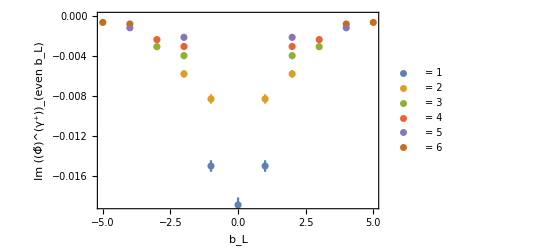

Fitting into

Fit dependence in  space

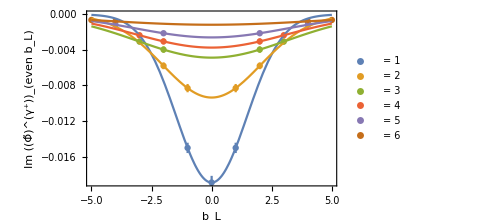

{-0.0189295 ⅇ^(-0.230778 b_L^2),-0.00936145 ⅇ^(-0.120002 b_L^2),-0.0048713 ⅇ^(-0.0514808 b_L^2),-0.00373954 ⅇ^(-0.0514439 b_L^2),-0.00259416 ⅇ^(-0.0497592 b_L^2),-0.00116781 ⅇ^(-0.0245821 b_L^2)}

```mathematica
PlotbLbT[sideNumForPlusvT = 20, sideNumForMinusvT = 25]
```